Part::partw: Part 2 of {1186.5803.79} does not exist.

FittedModel[…]

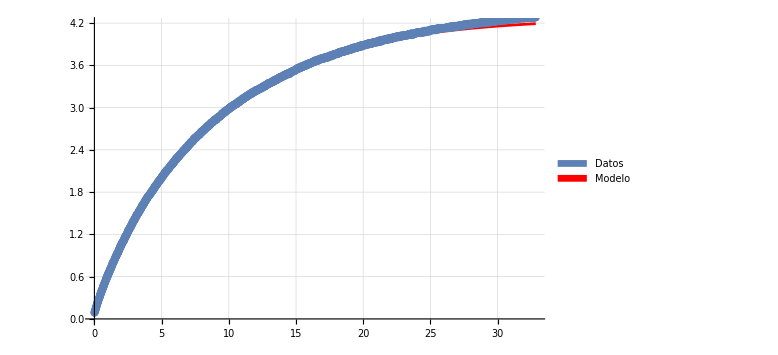

```mathematica
filePath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 2\\data\\medidas_grupales_paralelo_44Mohm\\carga";
fileName = "carga5paralelo.csv";
fullFileName = StringJoin[{filePath, "\\", fileName}];

(*Last datapoints may be missing second coordinate. We'll filter out these datapoints.*)
data = Import[fullFileName, "Data"][[;;-2]];
(*Filter voltages below startingVoltage*)
startingVoltage = 0.08;
maxVoltage = 5;
(*Cut points that have a voltage greater than maxVoltage - maxVoltage/e (that is, we'll remove all the points that are maxVoltage/e away from full charge).*)
cutOffPoint = maxVoltage - maxVoltage/7;
(*Filter*)
data = Select[data, #[[2]] > startingVoltage && #[[2]] < cutOffPoint&];
(*We shift all points in order to have starting voltage at time = 0.*)
data = MapAt[# - data[[1, 1]]&, data, {All, 1}];
(*We also shift all points downwards, so that the maximum voltage achieved within this time frame is at zero.
This'll make the fit easier. Afterwards we'll shift everything upwards, including the fit.*)
voltageShift = data[[-1, 2]];
data = MapAt[# - voltageShift&, data, {All, 2}];

model = V0 E^(k t);
fitModel = NonlinearModelFit[data, model, {V0, k}, t]

(*We shift the data back up.*)
data = MapAt[# + voltageShift&, data, {All, 2}];
dataPlot = ListPlot[data, PlotStyle->PointSize[0.01]];
(*We graph the model until the last point time and shift it back up.*)
modelGraph = Plot[fitModel[t] + voltageShift, {t, 0, data[[-1, 1]]}, PlotStyle->Red, TicksStyle->Directive[FontFamily->"Times New Roman", FontColor->Black]];

(*Customized full plot.*)
fullPlot = Show[modelGraph, dataPlot, Frame->Automatic,
FrameLabel->{Style["Tiempo (s)", 16, FontFamily->"Times New Roman", FontColor->Black], Style["Voltaje (V)", 16, FontFamily->"Times New Roman",FontColor->Black]}, FrameTicksStyle->Directive[FontSize->15, FontColor->Black, FontFamily->"Times New Roman"], GridLines->Automatic, GridLinesStyle->Directive[Dashed, RGBColor["#ccc"]], ImagePadding->{{55, 10}, {55, 10}}, ImageSize->Large];
fullPlot = Legended[fullPlot, Placed[SwatchLegend[{RGBColor["#5E81B5"], Red}, {"Datos", "Modelo"}, LabelStyle->{FontFamily->"Times New Roman", FontSize->14}, LegendFunction->Panel], {0.87, 0.84}]]

(*Export plot.*)
graphicsPath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 2\\graphics\\medidas_grupales_paralelo_44Mohm\\Carga";
graphicsName = StringJoin[{StringDelete[fileName, ".csv"], ".jpg"}];
fullGraphicsName = StringJoin[{graphicsPath, "\\", graphicsName}];
Export[fullGraphicsName, fullPlot];
```

```mathematica
measurementNumber =  StringDelete[StringDelete[fileName, "carga"], "paralelo.csv"];
predictedStartingVoltage = V0 /.fitModel["BestFitParameters"]; (*volts*)
fittedExponentParameter = k /. fitModel["BestFitParameters"];

fittedParameterFileFullPath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 2\\outputData\\EnParalelo\\Descarga\\EnParalelo_Descarga_FittedParameters.txt";
(*WriteString[fittedParameterFileFullPath, "Medicion,Voltaje Inicial Modelo,Exponente Modelo\n"];*)
WriteString[fittedParameterFileFullPath, measurementNumber, ",", predictedStartingVoltage,",", fittedExponentParameter, "\n"];
```

```mathematica
Close[fittedParameterFileFullPath];
```

```mathematica
"C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 2\\outputData\\EnParalelo\\Carga\\EnParalelo_Carga_FittedParameters.txt"
```

```mathematica
measuredStartingVoltage = data[[1, 2]]; (*volts*)
(*Time for starting voltage to drop by 1/e.*)
predictedDecayTime = 1/-k /.fitModel["BestFitParameters"]; (*seconds*)
measuredDecayTime = data[[-1, 1]]; (*seconds*)
(*Decay time is of the form RC (capacitance times resistance), so dividing by R yields C.*)
measuredResistance = 44000000; (*ohms*)
predictedCapacitance = predictedDecayTime / measuredResistance; (*farads*)
predictedNanoCapacitance = predictedCapacitance * 10^9; (*nanofarads*)

outputDataFileFullPath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 2\\outputData\\EnParalelo\\Carga\\EnParalelo_Carga_OutputData.txt";
(*WriteString[outputDataFileFullPath, "Medicion,Voltaje Inicial Modelo,Voltaje Inicial Arduino,Tiempo Decaimiento Modelo,Tiempo Decaimiento Arudino,Resistencia,NanoCapacitancia\n"];*)
WriteString[outputDataFileFullPath, measurementNumber, ",", predictedStartingVoltage,",", measuredStartingVoltage, ",", predictedDecayTime, ",", measuredDecayTime, ",", measuredResistance, ",", predictedNanoCapacitance, "\n"];
```

```mathematica
Close[outputDataFileFullPath];
```